# MATH 263 Numerical differential equations

Ethan Smith

## Lecture 1: Direction fields 4 FEB 2021

## Assigned reading for next time.

Zill, Section 2.6.

## General tips.

Get comfortable with idea of solving your own problems by reading help documentation.  It is a far more valuable skill than learning how to solve complicated problems in any particular computational package/language.  It’s the only skill that I can guarantee will generalize to all other computational tools.

Everything that the Wolfram Language does can be thought of as derived from its ability to apply general transformation rules to arbitrary symbolic expressions.  This unique feature makes the language very powerful, but it also makes it awkward to use unless you adapt to the mindset.  The ReplaceAll routine or /. operator is useful for accessing expressions that are returned as “replacement rules” (e.g., the results of a call to Solve or DSolve).

Whenever possible intermediate results should be appropriately stored and accessed.  Your code will be much more powerful and easy to modify for new situations.  In particular, try to avoid the very bad habit of copying output and pasting it as input into another cell.  Retyping is less dangerous than cut/paste, but is still very limiting.

Mathematica’s % operator can be a useful shortcut for accessing the result of the calculation which immediately precedes it in time, not in space.  Overuse can create confusing and unreadable code that often breaks.  You may see me use it on occasion in class, but it should never be used in “finished work” to be turned in.

## Direction fields via VectorPlot.

Given a first order ODE (ordinary differential equation)

y’ = f(x,y)

the function f(x,y) can be interpreted as the slope of the tangent line to any solution y whose graph passes through the point (x,y).  A direction field (or slope field) is a collection of short line segments in the plane so that the slope of the line segment at (x,y) is  f(x,y).  Any solution to the differential equation will necessarily be tangent to any line segment that it intersects, and so the direction field provides a useful (though perhaps incomplete) visualization of the solution set.

Note: Many people prefer the direction field objects to be line segments (not arrows) and have uniform length/color.

Consider the ODE (ordinary differential equation) y' = y.

Use the VectorPlot command with default options to create a direction field for the ODE.

```mathematica
?VectorPlot
```

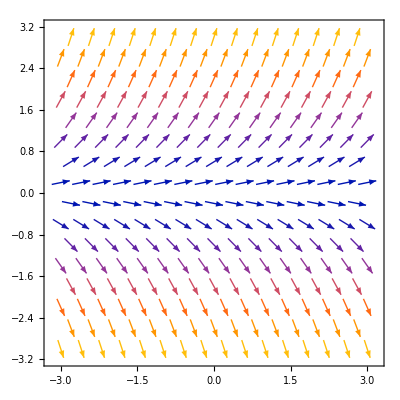

```mathematica
{a,b}={-3,3};
{c,d}={-3,3};
Clear[x,y] (* Here we want to use x and y as "placeholder symbols/variables."  It is good practice to make sure they are clear. *)
f[x_,y_]=y;
VectorPlot[{1,f[x,y]},{x,a,b},{y,c,d}]
```

Many people prefer direction field objects to be line segments (not arrows) and have uniform length/color.  By setting the appropriate VectorPlot options, create a direction field that salsifies these requirements.

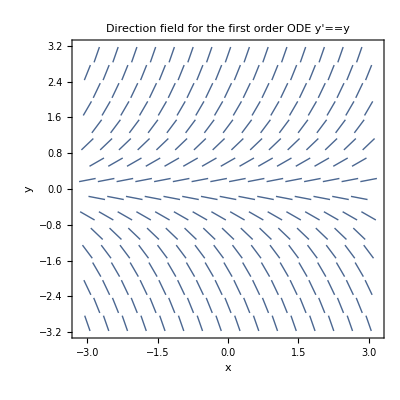

```mathematica
VectorPlot[{1,f[x,y]},{x,a,b},{y,c,d},VectorColorFunction->None,VectorStyle->Arrowheads[0],PlotLabel->StringForm["Direction field for the first order ODE ``",y'==f[x,y]],FrameLabel->{x,y}]
(*Note: In Mathematica 12, VectorPlot produces vectors of uniform length by default.  See VectorScale for Mathematica 11 (and lower). *)
```

Repeat the previous exercise for the ODE y' = x + y.

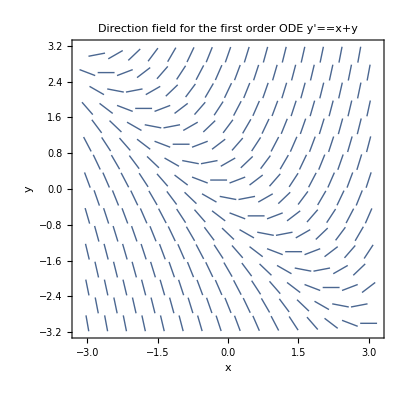

```mathematica
{a,b}={-3,3};
{c,d}={-3,3};
Clear[x,y]
f[x_,y_]=x+y;
VectorPlot[{1,f[x,y]},{x,a,b},{y,c,d},VectorColorFunction->None,VectorStyle->Arrowheads[0],PlotLabel->StringForm["Direction field for the first order ODE ``",y'==f[x,y]],FrameLabel->{x,y}]
```

## Exact solutions via DSolve.

Consider the ODE y' = y once again.

Guess a solution (or family of solutions) to the ODE.  If you know a valid analytic technique, feel free to use it.

We already know that the function y(x) = e^x is its own derivative.  Therefore, any solution of the form y(x) = C e^x is a solution to the ODE, where C is an arbitrary constant.

Use the DSolve command to compute the general solution.

```mathematica
?DSolve
```

```mathematica
Clear[x,y]
f[x_,y_]=y;
genSolnRule=DSolve[y'[x]==f[x,y[x]],y[x],x]
genY[x_]=y[x]/.genSolnRule[[1]] (* Notice how I'm using the /. (ReplaceAll) operator to access the result and create a function handle for the general solution. *)
```

{{y[x]→ⅇ^x C[1]}}

ⅇ^x C[1]

Extract the particular solution when the parameter C = 1 and plot its graph on top of a direction field over the interval [-3,3].

```mathematica
parY[x_]=genY[x]/.{C[1]->1}
{a,b}={-3,3};
{c,d}={0,20};
Show[
Plot[parY[x],{x,a,b},AxesLabel->{x,y},PlotStyle->Thick,PlotLabels->TraditionalForm[y[x]==parY[x]]],
VectorPlot[{1,f[x,y]},{x,a,b},{y,c,d},VectorColorFunction->None,VectorStyle->{Arrowheads[0],Red}],PlotRange->All
]
```

ⅇ^x

-Graphics-

Plot the family of solutions for C running from -10 to 10 in step size of 1.  Plot the curves in gray and (always) label your axes.

{-10 ⅇ^x,-9 ⅇ^x,-8 ⅇ^x,-7 ⅇ^x,-6 ⅇ^x,-5 ⅇ^x,-4 ⅇ^x,-3 ⅇ^x,-2 ⅇ^x,-ⅇ^x,0,ⅇ^x,2 ⅇ^x,3 ⅇ^x,4 ⅇ^x,5 ⅇ^x,6 ⅇ^x,7 ⅇ^x,8 ⅇ^x,9 ⅇ^x,10 ⅇ^x}

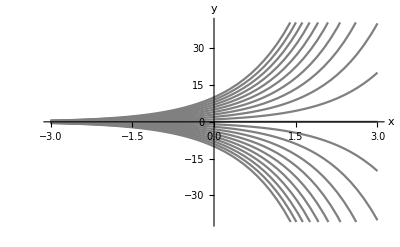

```mathematica
{a,b}={-3,3};
famY=Table[genY[x]/.{C[1]->c},{c,-10,10,1}]
famPlot=Plot[famY,{x,a,b},AxesLabel->{x,y},PlotStyle->Gray]
```

Solve the initial value problem (IVP) consisting of the ODE together with the initial condition y(2) = -10.  Plot this particular solution together with the initial condition point superimposed on the family plot above.

-10 ⅇ^(-2+x)

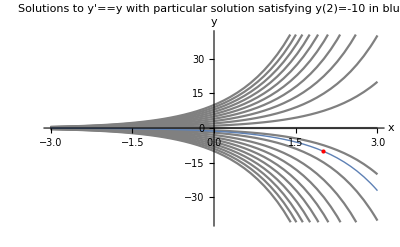

```mathematica
{x0,y0}={2,-10};
parY[x_]=y[x]/.DSolve[{y'[x]==f[x,y[x]],y[x0]==y0},y[x],x][[1]]

Show[
famPlot,
Plot[parY[x],{x,a,b},PlotStyle->Thick],
Graphics[{Red,PointSize[Large],Point[{x0,y0}]}],
PlotLabel->StringForm["Solutions to `` with particular solution satisfying y(``)=`` in blue.",y'==f[x,y],x0,y0]
]
```

Repeat the previous exercise for the ODE y' = x + y.

To solve the equation by hand, we might recognize that it is first order linear, but nonhomogeneous.  Rewriting the equation as

y’ - y = x

we see that the AHE (associated homogenous equation) is y' - y = 0.   We already saw that y_c = C e^x is the solution set to this equation.  Next we look for a particular solution to the nonhomogeneous equation.  Either using the method of undetermined coefficients or just guessing we arrive at the solution y_p = -x-1, which works because

y_p' - y_p = -1 - (-x-1) = x.

The general solution is then y(x) = y_c + y_p = C e^x -x - 1.

```mathematica
Clear[x,y]
f[x_,y_]=x+y;
genSolnRule=DSolve[y'[x]==f[x,y[x]],y[x],x];
genY[x_]=y[x]/.genSolnRule[[1]]
```

-1-x+ⅇ^x C[1]

```mathematica
parY[x_]=genY[x]/.C[1]->1
{a,b}={-3,3};
{c,d}={0,8};
Show[
Plot[parY[x],{x,a,b},AxesLabel->{x,y},PlotStyle->Thick,PlotLabels->TraditionalForm[y[x]==parY[x]]],
VectorPlot[{1,f[x,y]},{x,a,b},{y,c,d},VectorColorFunction->None,VectorStyle->{Arrowheads[0],Red}],PlotLabel->TraditionalForm[y'==f[x,y]]
]
```

-1+ⅇ^x-x

-Graphics-

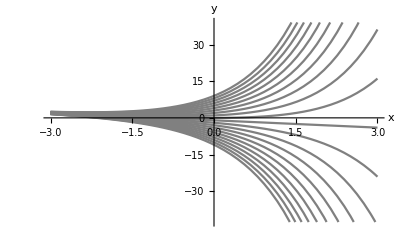

```mathematica
famY=Table[genY[x]/.{C[1]->c},{c,-10,10,1}];
famPlot=Plot[famY,{x,a,b},AxesLabel->{x,y},PlotStyle->Gray]
```

-(ⅇ^2+7 ⅇ^x+ⅇ^2 x)/ⅇ^2

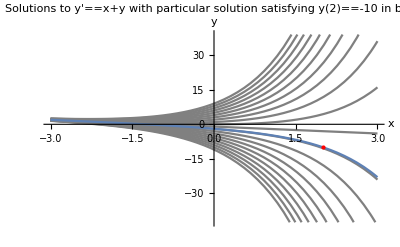

```mathematica
{x0,y0}={2,-10};
parY[x_]=y[x]/.DSolve[{y'[x]==f[x,y[x]],y[x0]==y0},y[x],x][[1]]

Show[
famPlot,
Plot[parY[x],{x,a,b}],
Graphics[{Red,PointSize[Large],Point[{x0,y0}]}],
PlotLabel->StringForm["Solutions to ``\n with particular solution satisfying `` in blue.",TraditionalForm[y'==f[x,y]],y[x0]==y0]
]
```

Consider the ODE y'' = y.

Use DSolve to compute the general solution.

```mathematica
f[x_,y_]=y;
genSolnRule=DSolve[y''[x]==f[x,y[x]],y[x],x]
genY[x_]=y[x]/.genSolnRule[[1]]
```

{{y[x]→ⅇ^x C[1]+ⅇ^-x C[2]}}

ⅇ^x C[1]+ⅇ^-x C[2]

Sometimes Mathematica produces solutions in a form that we may not expect or prefer.  Apply the routine TrigToExp or ExpToTrig (whichever seems appropriate) to transform the solution into an alternate form.  Then use Collect to express the result as a linear combination of the alternate “basis.”

```mathematica
Collect[ExpToTrig[genY[x]],{Cosh[x],Sinh[x]}]
```

(C[1]+C[2]) Cosh[x]+(C[1]-C[2]) Sinh[x]

Repeat the previous exercise for the ODE y'' = -y.

```mathematica
f[x_,y_]=-y;
genSolnRule=DSolve[y''[x]==f[x,y[x]],y[x],x]
genY[x_]=y[x]/.genSolnRule[[1]]
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]}}

C[1] Cos[x]+C[2] Sin[x]

```mathematica
Collect[TrigToExp[genY[x]],{Exp[I*x],Exp[-I*x]}]
```

ⅇ^(ⅈ x) (C[1]/2-(ⅈ C[2])/2)+ⅇ^(-ⅈ x) (C[1]/2+(ⅈ C[2])/2)

Consider the ODE y' = e^(-x^2).

Can you solve this one by hand?

Not really.  Clearly, we need y = ∫ⅆy = ∫e^(-x^2)ⅆx, which seems pretty impossible.

Can DSolve do it?  If so, plot the particular solution satisfying y(0) = 1 over the interval [-3,3].

```mathematica
f[x_,y_]=Exp[-x^2];
genSolnRule=DSolve[y'[x]==f[x,y[x]],y[x],x]
genY[x_]=y[x]/.genSolnRule[[1]]
```

{{y[x]→C[1]+1/2 √π Erf[x]}}

C[1]+1/2 √π Erf[x]

```mathematica
{x0,y0}={0,1};
{a,b}={-3,3};
parY[x_]=y[x]/.DSolve[{y'[x]==f[x,y[x]],y[x0]==y0},y[x],x][[1]]
Plot[parY[x],{x,a,b},AxesLabel->{x,y},PlotLabels->TraditionalForm[y[x]==parY[x]],PlotLabel->StringForm["Solution to the IVP ``, ``",TraditionalForm[y'==f[x,y]],y[x0]==y0]]
```

1/2 (2+√π Erf[x])

-Graphics-

The answer to the question, can DSolve solve this problem is both “yes, and no.”  We have to expand our notion of what it means to “solve” a problem.  DSolve says that the solution is essentially the “error function.”  More precisely, it is telling us that the general solution is

y(x) = C + ∫_0^x e^(-t^2)ⅆt.

In a sense, this is just inventing a name for the solution that we know (by the fundamental theorem of calculus) must exist.  In general, we have no way of evaluating this function exactly because we have no elementary antiderivative for the integrand e^(-x^2).  This apparent problem obviates the need to develop numerical techniques.

Note: Depending on who taught you calc II, you should already be familiar with the idea of defining functions as solutions to problems that we know ought to exist.  The “true” definition of the natural logarithm is as the solution to the IVP y' = 1/x, y(1) = 0, i.e.,

log(x) = ∫_1^x 1/t ⅆt.

We only know how to evaluate it exactly at certain “special values” of x.  All other values must be approximated by numerical techniques.